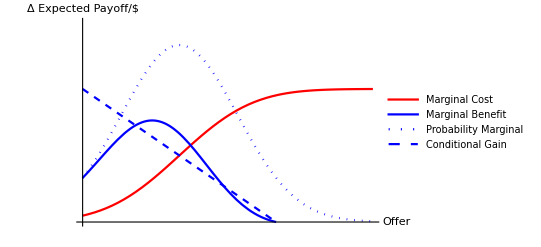

C:\Users\ssayre\Documents\activeProjectRepositories\esvcsV2\text\baseMBvMC.eps

```mathematica
gamma[sigShr_]:=Sqrt[sigShr]
signal[sigZ_,sigShr_,sEnv_]:=sigZ/gamma[sigShr]/sEnv
rhoSeRp[sigShr_,sEnv_,rhoRatio_,rhoEnvRp_]:=rhoRatio*gamma[sigShr]*rhoEnvRp+(1-rhoRatio)*rhoEnvRp*(1-Sqrt[1-sigShr])/gamma[sigShr]
condMeanP[sigZ_,sigShr_,sEnv_,sRp_,rhoRatio_,rhoEnvRp_,meanP_]:=meanP+sRp *rhoSeRp[sigShr,sEnv,rhoRatio,rhoEnvRp]/gamma[sigShr]/sEnv*signal[sigZ,sigShr,sEnv]
condSigP[sRp_,sigShr_,sEnv_,sRp_,rhoRatio_,rhoEnvRp_]:=sRp*Sqrt[1-rhoSeRp[sigShr,sEnv,rhoRatio,rhoEnvRp]]
sReRp[sEnv_,sRp_,rhoEnvRp_,sigShr_,rhoRatio_]:=sEnv*sRp*(rhoEnvRp-gamma[sigShr]*rhoSeRp[sigShr,sEnv,rhoRatio,rhoEnvRp])
a[meanE_,meanP_,sigZ_,sigShr_,sEnv_,sRp_,rhoEnvRp_,rhoRatio_]:=meanE+signal[sigZ,sigShr,sEnv]-sReRp[sEnv,sRp,rhoEnvRp,sigShr,rhoRatio]*condMeanP[sigZ,sigShr,sEnv,sRp,rhoRatio,rhoEnvRp,meanP]/(condSigP[sRp,sigShr,sEnv,sRp,rhoRatio,rhoEnvRp]^2)
pA[x_,meanE_,meanP_,sigZ_,sigShr_,sEnv_,sRp_,rhoEnvRp_,rhoRatio_]:=CDF[NormalDistribution[condMeanP[sigZ,sigShr,sEnv,sRp,rhoRatio,rhoEnvRp,meanP],condSigP[sRp,sigShr,sEnv,sRp,rhoRatio,rhoEnvRp]],x]
pM[x_,meanE_,meanP_,sigZ_,sigShr_,sEnv_,sRp_,rhoEnvRp_,rhoRatio_]:=PDF[NormalDistribution[condMeanP[sigZ,sigShr,sEnv,sRp,rhoRatio,rhoEnvRp,meanP],condSigP[sRp,sigShr,sEnv,sRp,rhoRatio,rhoEnvRp]],x]
condGain[x_,meanE_,meanP_,sigZ_,sigShr_,sEnv_,sRp_,rhoEnvRp_,rhoRatio_]:=a[meanE,meanP,sigZ,sigShr,sEnv,sRp,rhoEnvRp,rhoRatio]-x+x*sReRp[sEnv,sRp,rhoEnvRp,sigShr,rhoRatio]/(condSigP[sRp,sigShr,sEnv,sRp,rhoRatio,rhoEnvRp]^2)
MB[x_,meanE_,meanP_,sigZ_,sigShr_,sEnv_,sRp_,rhoEnvRp_,rhoRatio_]:=pM[x,meanE,meanP,sigZ,sigShr,sEnv,sRp,rhoEnvRp,rhoRatio]*condGain[x,meanE,meanP,sigZ,sigShr,sEnv,sRp,rhoEnvRp,rhoRatio]
rpf[x_,meanE_,meanP_,sigZ_,sigShr_,sEnv_,sRp_,rhoEnvRp_,rhoRatio_]:=pA[x,meanE,meanP,sigZ,sigShr,sEnv,sRp,rhoEnvRp,rhoRatio]*(meanE+signal[sigZ,sigShr,sEnv]-x)-sReRp[sEnv,sRp,rhoEnvRp,sigShr,rhoRatio]*pM[x,meanE,meanP,sigZ,sigShr,sEnv,sRp,rhoEnvRp,rhoRatio]

baseMeanE = 1; baseMeanP=.5; baseSEnv=1.5; baseSrp = .3; baseSigShr=.5; baseRhoRatio=.5;xMax =1.5;yRange={0,1.5};
plotStyleList = {Red,{Red,Dotted},{Red,Dashed},Blue,{Blue,Dotted},{Blue,Dashed}};
plotStyleList = {Red,Blue};
sigZVals = {-.5,0,.5};
baseMBvMCplot=Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio]},
{x,0,xMax},PlotStyle->{Red,Blue,{Blue,Dotted},{Blue,Dashed}},PlotRange->yRange,Ticks->None,PlotLegends->{"Marginal Cost","Marginal Benefit","Probability Marginal","Conditional Gain"},AxesLabel->{ "Offer","Δ Expected Payoff/$"}]
Export["C:\\Users\\ssayre\\Documents\\activeProjectRepositories\\esvcsV2\\text\\baseMBvMC.eps",baseMBvMCplot,"EPS"]
```

## MB/MC Grid

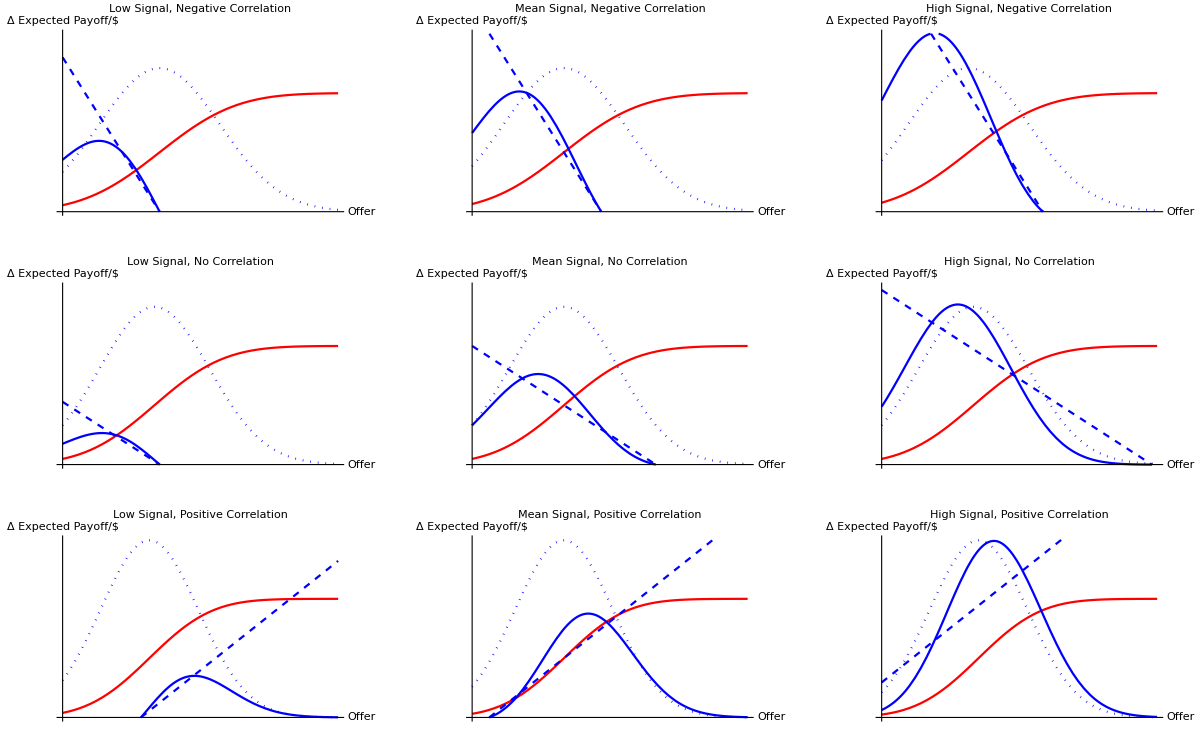

```mathematica
baseRhoRatio = 0;plotStyleList={Red,Blue,{Blue,Dotted},{Blue,Dashed}}; yRange={0,1.5}; sigZVals={-.5,0,.5};plotOptions = {PlotStyle->plotStyleList,PlotRange->yRange,Ticks->None,AxesLabel->{"Offer","Δ Expected Payoff/$"}};
GraphicsGrid[{
{Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
MB[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],pM[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],condGain[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Low Signal, Negative Correlation"],
Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Mean Signal, Negative Correlation"],
Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
MB[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],pM[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],condGain[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"High Signal, Negative Correlation"]},

{Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
MB[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],pM[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],condGain[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Low Signal, No Correlation"],
Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Mean Signal, No Correlation"],
Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
MB[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],pM[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],condGain[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"High Signal, No Correlation"]},

{Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio],
MB[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio],pM[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio],condGain[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Low Signal, Positive Correlation"],
Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio],
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio],pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio],condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Mean Signal, Positive Correlation"],
Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio],
MB[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio],pM[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio],condGain[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"High Signal, Positive Correlation"]}}
,ImageSize->Full]
```

## Marginal Cost

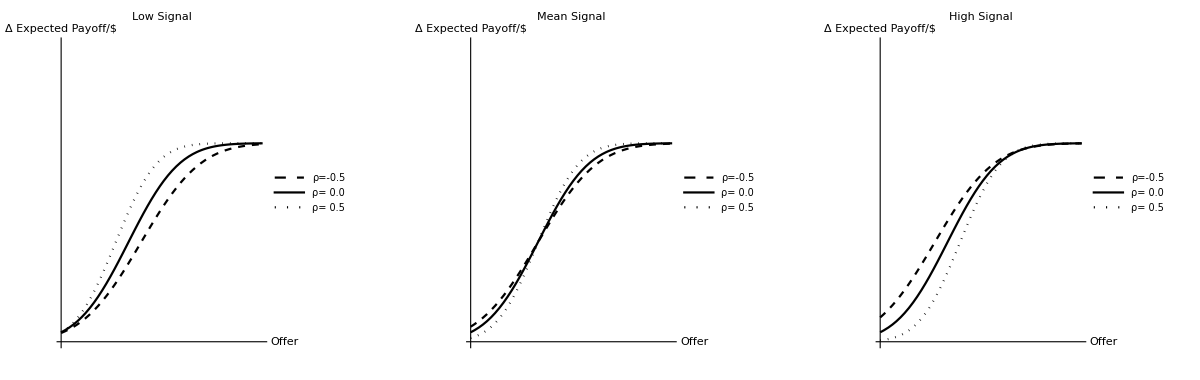

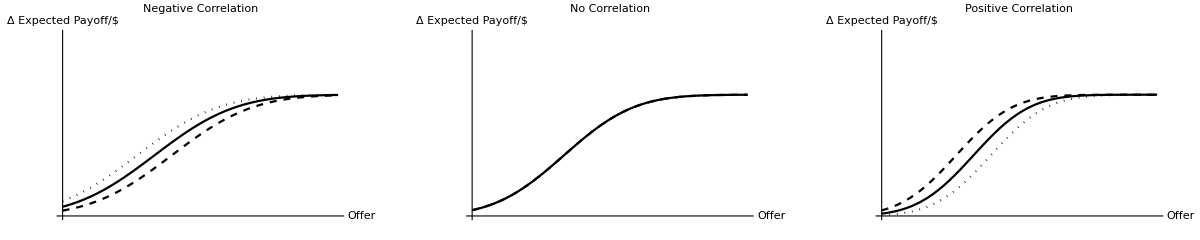

```mathematica
plotStyleList={{Black,Dashed},Black,{Black,Dotted}}; yRange={0,1.5}; sigZVals={-1,0,1}; baseRhoRatio=1;plotOptions = {PlotStyle->plotStyleList,PlotRange->yRange,Ticks->None,AxesLabel->{"Offer","Δ Expected Payoff/$"}};
MCbySignal =GraphicsRow[{
Plot[{
pA[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
pA[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
pA[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Low Signal",PlotLegends-> Placed[{"ρ=-0.5","ρ= 0.0","ρ= 0.5"},{Scaled[{.65,.5}],{0,.5}}]],
Plot[{
pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Mean Signal",PlotLegends-> Placed[{"ρ=-0.5","ρ= 0.0","ρ= 0.5"},{Scaled[{.65,.5}],{0,.5}}]],
Plot[{
pA[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
pA[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
pA[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"High Signal",PlotLegends-> Placed[{"ρ=-0.5","ρ= 0.0","ρ= 0.5"},{Scaled[{.65,.5}],{0,.5}}]]
}
,ImageSize->Full]
MCbyCorrelation=GraphicsRow[{
Plot[{
pA[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
pA[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Negative Correlation"],
Plot[{
pA[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
pA[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"No Correlation"],
Plot[{
pA[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio],
pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio],
pA[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Positive Correlation"]}
,ImageSize->Full]
```

```mathematica
Export["C:\\Users\\ssayre\\Documents\\activeProjectRepositories\\esvcsV2\\text\\testMC.eps",MCbyCorrelation,"EPS"]
```

C:\Users\ssayre\Documents\activeProjectRepositories\esvcsV2\text\testMC.eps

```mathematica
Export["C:\\Users\\ssayre\\Documents\\activeProjectRepositories\\esvcsV2\\text\\deltaMC.eps",MCbyCorrelation,"EPS"]
```

C:\Users\ssayre\Documents\activeProjectRepositories\esvcsV2\text\deltaMC.eps

## Probability Marginal

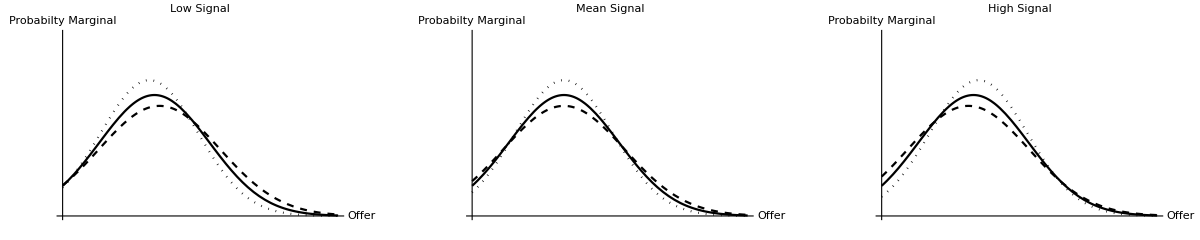

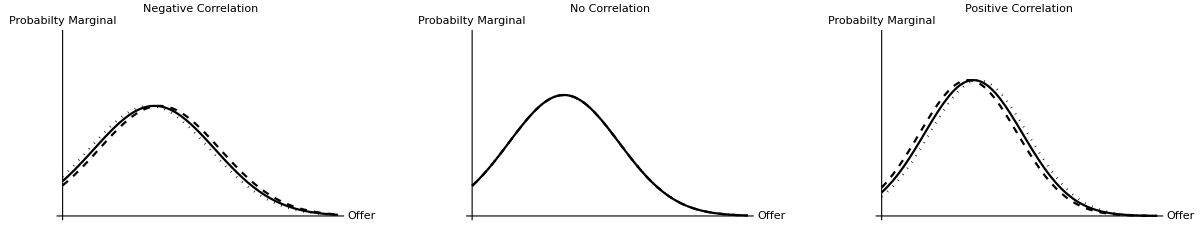

C:\Users\ssayre\Documents\activeProjectRepositories\esvcsV2\text\deltaPM.eps

```mathematica
plotStyleList={{Black,Dashed},Black,{Black,Dotted}}; yRange={0,2}; sigZVals={-.5,0,.5}; baseRhoRatio = 0;plotOptions = {PlotStyle->plotStyleList,PlotRange->yRange,Ticks->None,AxesLabel->{"Offer","Probabilty Marginal"}};
prMbySignal=GraphicsRow[{
Plot[{
pM[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
pM[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
pM[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Low Signal"],
Plot[{
pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Mean Signal"],
Plot[{
pM[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
pM[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
pM[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"High Signal"]
}
,ImageSize->Full]
pMbyCorrelation=GraphicsRow[{
Plot[{
pM[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
pM[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Negative Correlation"],
Plot[{
pM[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
pM[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"No Correlation"],
Plot[{
pM[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio],
pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio],
pM[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Positive Correlation"]}
,ImageSize->Full]
Export["C:\\Users\\ssayre\\Documents\\activeProjectRepositories\\esvcsV2\\text\\deltaPM.eps",pMbyCorrelation,"EPS"]
```

## Conditional Gain

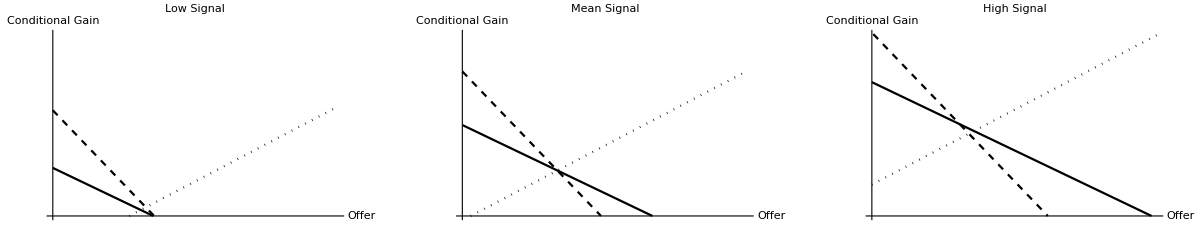

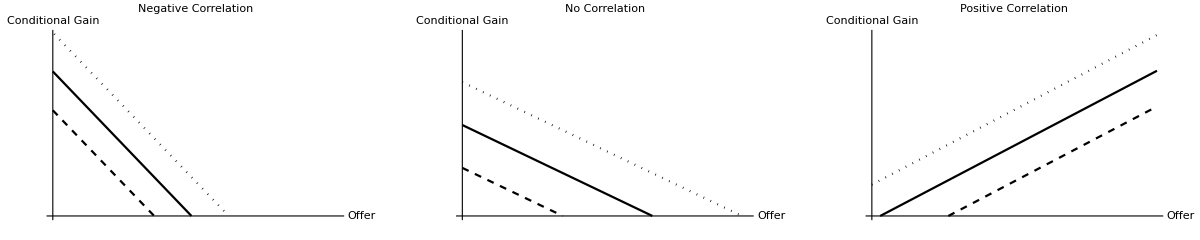

C:\Users\ssayre\Documents\activeProjectRepositories\esvcsV2\text\deltaCondGain.eps

```mathematica
plotStyleList={{Black,Dashed},Black,{Black,Dotted}}; yRange={0,2}; sigZVals={-.5,0,.5};plotOptions = {PlotStyle->plotStyleList,PlotRange->yRange,Ticks->None,AxesLabel->{"Offer","Conditional Gain"}};
condGainBySignal=GraphicsRow[{
Plot[{
condGain[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
condGain[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
condGain[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Low Signal"],
Plot[{
condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Mean Signal"],
Plot[{
condGain[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
condGain[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
condGain[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"High Signal"]
}
,ImageSize->Full]
condGainByCorrelation=GraphicsRow[{
Plot[{
condGain[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
condGain[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Negative Correlation"],
Plot[{
condGain[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
condGain[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"No Correlation"],
Plot[{
condGain[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio],
condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio],
condGain[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Positive Correlation"]}
,ImageSize->Full]
Export["C:\\Users\\ssayre\\Documents\\activeProjectRepositories\\esvcsV2\\text\\deltaCondGain.eps",condGainByCorrelation,"EPS"]
```

## Marginal Benefit

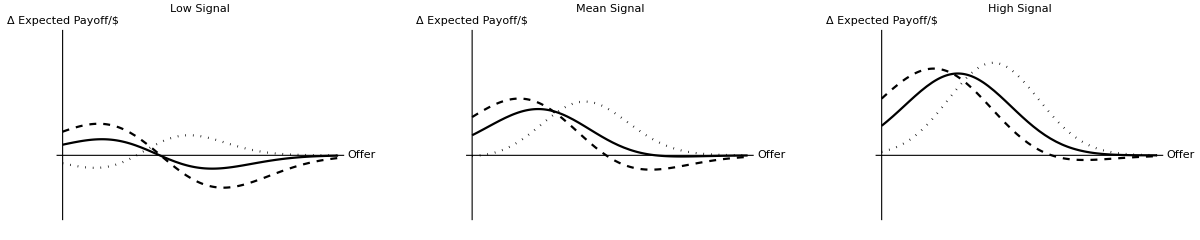

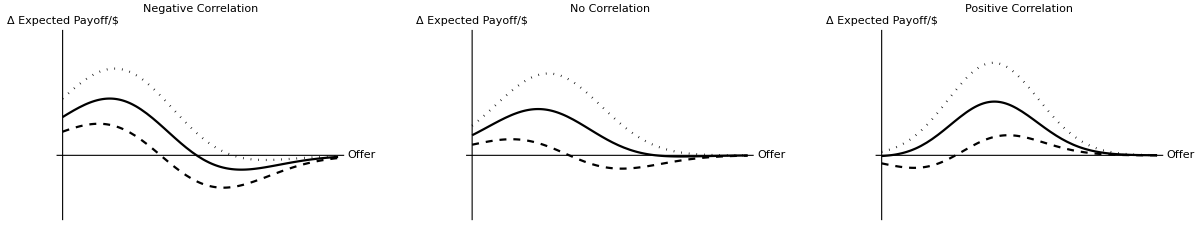

C:\Users\ssayre\Documents\activeProjectRepositories\esvcsV2\text\deltaMB.eps

```mathematica
plotStyleList={{Black,Dashed},Black,{Black,Dotted}}; yRange={-1,2}; sigZVals={-.5,0,.5};plotOptions = {PlotStyle->plotStyleList,PlotRange->yRange,Ticks->None,AxesLabel->{"Offer","Δ Expected Payoff/$"}};
MBbySignal=GraphicsRow[{
Plot[{
MB[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
MB[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
MB[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Low Signal"],
Plot[{
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Mean Signal"],
Plot[{
MB[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
MB[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
MB[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"High Signal"]
}
,ImageSize->Full]
MBbyCorrelation=GraphicsRow[{
Plot[{
MB[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
MB[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Negative Correlation"],
Plot[{
MB[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
MB[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"No Correlation"],
Plot[{
MB[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio],
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio],
MB[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Positive Correlation"]}
,ImageSize->Full]
Export["C:\\Users\\ssayre\\Documents\\activeProjectRepositories\\esvcsV2\\text\\deltaMB.eps",MBbyCorrelation,"EPS"]
```

## Regulator Payoff Function

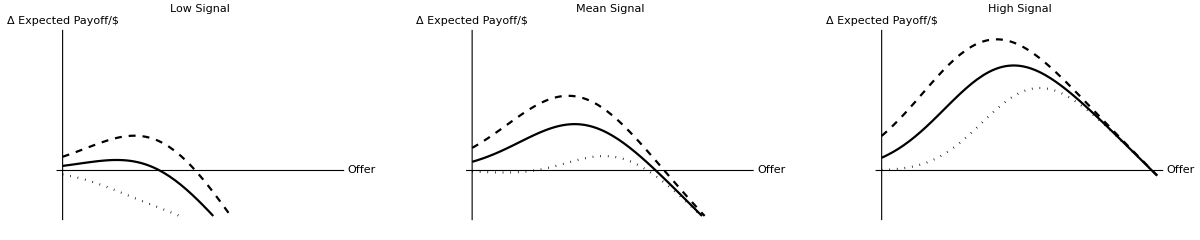

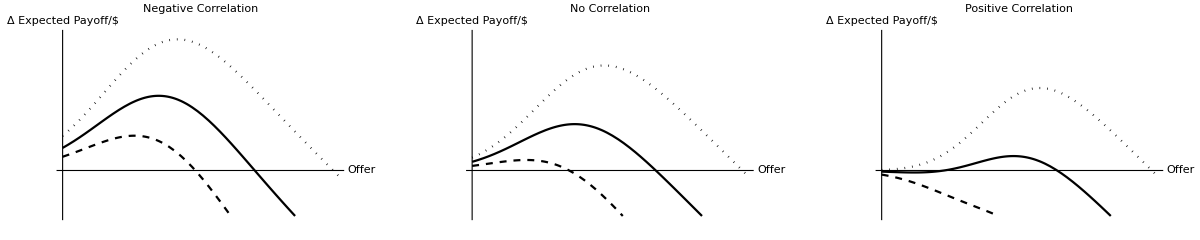

C:\Users\ssayre\Documents\activeProjectRepositories\esvcsV2\text\deltaPayoff.eps

```mathematica
plotStyleList={{Black,Dashed},Black,{Black,Dotted}}; yRange={-.25,.75}; sigZVals={-.5,0,.5};plotOptions = {PlotStyle->plotStyleList,PlotRange->yRange,Ticks->None,AxesLabel->{"Offer","Δ Expected Payoff/$"}};
rpfbySignal=GraphicsRow[{
Plot[{
rpf[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
rpf[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
rpf[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Low Signal"],
Plot[{
rpf[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
rpf[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
rpf[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Mean Signal"],
Plot[{
rpf[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
rpf[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
rpf[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"High Signal"]
}
,ImageSize->Full]
rpfbyCorrelation=GraphicsRow[{
Plot[{
rpf[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
rpf[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio],
rpf[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,-.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Negative Correlation"],
Plot[{
rpf[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
rpf[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio],
rpf[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,0,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"No Correlation"],
Plot[{
rpf[x,baseMeanE,baseMeanP,sigZVals[[1]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio],
rpf[x,baseMeanE,baseMeanP,sigZVals[[2]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio],
rpf[x,baseMeanE,baseMeanP,sigZVals[[3]],baseSigShr,baseSEnv,baseSrp,.5,baseRhoRatio]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Positive Correlation"]}
,ImageSize->Full]
Export["C:\\Users\\ssayre\\Documents\\activeProjectRepositories\\esvcsV2\\text\\deltaPayoff.eps",rpfbyCorrelation,"EPS"]
```